```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zakk/Desktop/ISTAustria/AngulonDiagMC/Analysis

```mathematica
MyImport[fname_]:=Cases[Import[fname,"Table"],{_?NumberQ,___}];
```

```mathematica
{minτ,maxτ}={7,14};
```

```mathematica
prefixList={"m10","m9","m8","m7","m6","m5","m4","m3","m2","m1","0","1","2","3","4","5"};
```

```mathematica
prefixList={"m10","m9","m8","m7","m6","m5","m4","m3","m2","m1","1","2","3","4","5"};
```

```mathematica
readμ[fname_]:=ToExpression@First@With[{txt=ReadList[fname,String]},Flatten@StringCases[txt,"# Chemical potential: "~~(x:NumberString)->ToExpression@x]]
```

```mathematica
readlogn[prefix_]:=ToExpression@First@With[{txt=ReadList[prefix,String]},Flatten@StringCases[txt,"# Potential parameters: (logn) = ("~~(x:NumberString)->ToExpression@x]]
```

```mathematica
readavgorder[prefix_]:=ToExpression@First@With[{txt=ReadList[prefix,String]},Flatten@StringCases[txt,"# Average order: "~~(x:NumberString)->ToExpression@x]]
```

```mathematica
μs=Transpose[{readlogn["test"<>#<>".dat"]&/@prefixList,readμ["test"<>#<>".dat"]&/@prefixList}];
```

```mathematica
avgorders=Transpose[{readlogn["test"<>#<>".dat"]&/@prefixList,readavgorder["test"<>#<>".dat"]&/@prefixList}];
```

```mathematica
μ[logn_]:=First[Select[μs,#[[1]]==logn&]][[2]]
```

```mathematica
avgorder[logn_]:=First[Select[avgorders,#[[1]]==logn&]][[2]]
```

```mathematica
cList=Transpose[{prefixList,readlogn["test"<>#<>".dat"]&/@prefixList}];
```

```mathematica
dList={#[[2]],MyImport["test"<>#[[1]]<>".dat"]}&/@cList;
```

```mathematica
GetSingleList[logn_]:=First[Select[dList,#[[1]]==logn&]][[2]]
```

```mathematica
GetRawParameters[logn_]:=With[{data=GetSingleList[logn]},With[{refinedData=Select[data,minτ<#[[1]]<maxτ&]},NonlinearModelFit[{#[[1]],Log[#[[2]]]}&/@refinedData,q+m *x,{q,m},x]]]["BestFitParameters"]
```

```mathematica
GetParameters[logn_]:={z->Exp[q],En->μ[logn]-m}/.GetRawParameters[logn]
```

```mathematica
fData=With[{logns=#[[2]]&/@cList},{#,GetParameters[#],avgorder[#]}&/@logns];
```

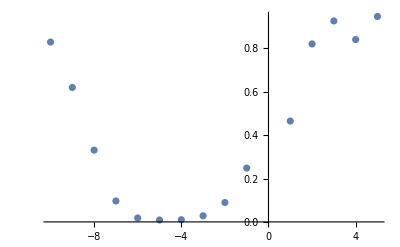

```mathematica
dmcP1=ListPlot[{#[[1]],z/.#[[2]]}&/@fData]
```

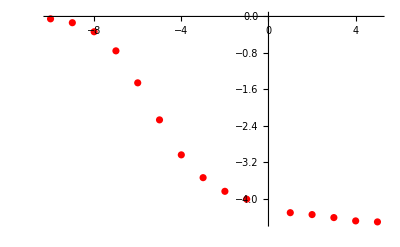

```mathematica
dmcP2=ListPlot[{#[[1]],En/.#[[2]]}&/@fData,PlotStyle->Red]
```

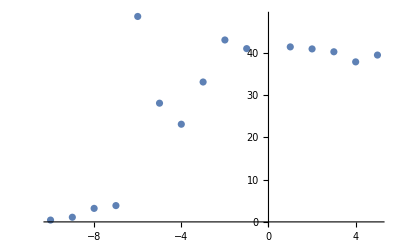

```mathematica
dmcP3=ListPlot[{#[[1]],#[[3]]}&/@fData]
```

Here we need to load the notebook SelfEnergies.nb

```mathematica
<<SelfEnergies.m
```

```mathematica
V[λ_,k_,{n_}]:=U[λ,k,{n}]Sqrt[(2*λ+1)/(4*π)]
```

```mathematica
Edef[n_]:=-NIntegrate[V[0,k,{n}]^2/ωk[k,{n}],{k,0,Infinity}]-NIntegrate[V[1,k,{n}]^2/ωk[k,{n}],{k,0,Infinity}]
```

```mathematica
scResult=ListPlot[Table[{logn,Edef[Exp[logn]]},{logn,-15,5,0.1}],Joined->True,PlotStyle->{Dashed,Red}];
```

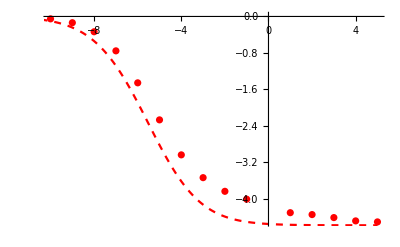

```mathematica
Show[dmcP2,scResult]
```

```mathematica
dataSpectral=Sort@Import["spectral1st.dat"];
```

```mathematica
dataSpectralSparse=Select[dataSpectral,(Abs[FractionalPart[10*#[[1]]]]<0.01)&&(Abs[FractionalPart[10*#[[2]]]]<0.01)&];
```

```mathematica
p1=ListDensityPlot[{#[[1]],#[[2]],1/(0.0001+#[[3]])^((1/10))}&/@dataSpectralSparse];
```

```mathematica
Show[p1,dmcP2,scResult]
```

-Graphics-